```mathematica
(* --------------   Tipping Model with white Noise ----------*)
TMCWN=List[];
Do[
Clear[x,F,t,tmax,zero,ans,data,Trend,NTrend,proc,n,F,t,s,noise,x2];
n=1000;
F=(2/n)*t -1;
noise=Interpolation[Table[{i,RandomReal[NormalDistribution[0,0.2]]},{i,0,n}]];
s=NDSolve[{x'[t]==-x[t]^3+x[t]-F+noise[t], x2'[t]==-x2[t]^3+x2[t]-F ,x[0]==1.25, x2[0]==1.25},{x,x2},{t,0,n}];
(*Plot[{Evaluate[x[t]/.s], Evaluate[x2[t]/.s]},{t,0,n},PlotRange->All,Epilog->{InfiniteLine[{600,0},{0,1}]}]*)
Clear[signal];
signal ={};
Do[
AppendTo[signal,Evaluate[x[i]/.s][[1]]],{i,0,600,1}];

TMCWN=AppendTo[TMCWN,signal]
,100]
```

```mathematica
(*Dimensions[TMCWN]*)
TM=Transpose[TMCWN]
```

{{1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25},599,{0.756269,99}}
 |  |  |  |

```mathematica
Dimensions[TM]
```

{601,100}

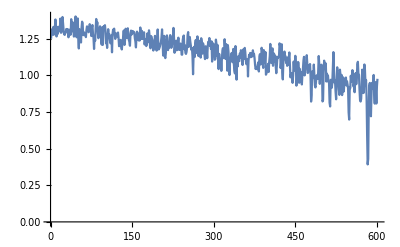

```mathematica
ListLinePlot[TMCWN[[5,All]]]
```

```mathematica
Export["/Users/lha305/Desktop//TMCWN.csv",TM]
```

/Users/lha305/Desktop//TMCWN.csv

```mathematica
(* --------------   Tipping Model with time dependent Red Noise ----------*)
```

```mathematica
bphi=RandomReal[{-0.9,0.9},500];
aphi=RandomReal[{-0.9,0.9},500];
Do[
aphi[[i]]=RandomReal[{-Min[bphi[[i]],0],(1-Max[bphi[[i]],0])},1][[1]],{i,1,500}]
```

```mathematica
TMTDRN=List[];
Do[
Clear[x,F,t,tmax,zero,ans,data,Trend,NTrend,proc,n,F,t,s,noise,x2];
Clear[n,noise,phi,sigma,no,phio,sigmao];
Clear[x,F,t,tmax,zero,ans,data,Trend,NTrend,proc,n,F,t,s,noise,x2,ARe,AR,noise2,noisew];
n=300;
F=(2/n)*t -1;
no=0;
phio = aphi[j];
sigmao=0.13;
noise ={};
Do[
AppendTo[noise,no];
phio =aphi[[j]]+((i*bphi[[j]])/n);
no = phio*no + RandomReal[NormalDistribution[0,sigmao]],
{i,0,n}];
cont=Interpolation[noise];
s=NDSolve[{x'[t]==-x[t]^3+x[t]-F+cont[t+1], x2'[t]==-x2[t]^3+x2[t]-F ,x[0]==1.25, x2[0]==1.25},{x,x2},{t,0,n}];
Clear[signal];
signal ={};
Do[
AppendTo[signal,Evaluate[x[i]/.s][[1]]],{i,0,200,1}];

TMTDRN=AppendTo[TMTDRN,signal];
,{j,1,500}]
```

{201,500}

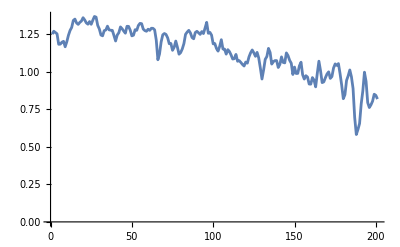

```mathematica
TM=Transpose[TMTDRN];
Dimensions[TM]
ListLinePlot[TM[[All,4]]]
```

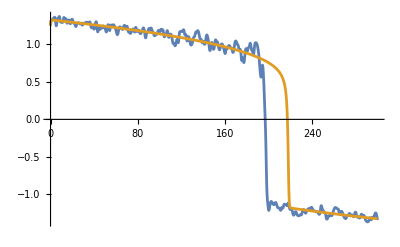

```mathematica
Plot[{Evaluate[x[t]/.s], Evaluate[x2[t]/.s]},{t,0,n},PlotRange->All,Epilog->{InfiniteLine[{500,0},{0,1}]}]
```

```mathematica
Export["/Users/lha305/Desktop//TMTDRN_150.csv",TM];
Export["/Users/lha305/Desktop//TMTDRN_a_150.csv",aphi];
Export["/Users/lha305/Desktop//TMTDRN_b_150.csv",bphi];
```

```mathematica
(* --------------   Non-Tipping Model with time dependent Red Noise ----------*)
```

```mathematica
bphi=RandomReal[{-0.9,0.9},100];
aphi=RandomReal[{-0.9,0.9},100];
Do[
aphi[[i]]=RandomReal[{-Min[bphi[[i]],0],(1-Max[bphi[[i]],0])},1][[1]],{i,1,100}]
```

```mathematica
NTMTDRN=List[];
Do[
Clear[n,noise,phi,sigma,no,phio,sigmao];
Clear[x,F,t,tmax,zero,ans,data,Trend,NTrend,proc,n,F,t,s,noise,x2,ARe,AR,noise2,noisew];
n=150;
noise ={};
no=0;
phio = aphi[j];
sigmao=1;
Do[
AppendTo[noise,no];
phio =aphi[[j]]+((i*bphi[[j]])/n);
no = phio*no + RandomReal[NormalDistribution[0,sigmao]],
{i,0,n}];
cont=Interpolation[noise];
s=NDSolve[{x'[t]==-5*x[t]+ cont[t+1], x2'[t]==-5*x2[t] ,x[0]==0, x2[0]==0},{x,x2},{t,0,n}];
Clear[signal];
signal ={};
Do[
AppendTo[signal,Evaluate[x[i]/.s][[1]]],{i,0,150,1/2}];

NTMTDRN=AppendTo[NTMTDRN,signal];
,{j,1,100}]
```

{301,100}

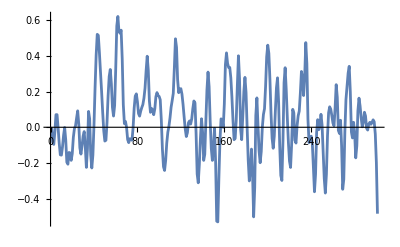

```mathematica
TM=Transpose[NTMTDRN];
Dimensions[TM]
ListLinePlot[TM[[All,1]]]
```

```mathematica
Export["/Users/lha305/Desktop//NTMTDRN_2.csv",TM];
Export["/Users/lha305/Desktop//NTMTDRN_a_2.csv",aphi];
Export["/Users/lha305/Desktop//NTMTDRN_b_2.csv",bphi];
```

```mathematica
(* --------------   Non tipping Model Constant Red Noise ----------*)
NTMCRN=List[];
Do[
Clear[n,noise,phi,sigma,no,phio,sigmao];
Clear[x,F,t,tmax,zero,ans,data,Trend,NTrend,proc,n,F,t,s,noise,x2,ARe,AR,noise2,noisew];
n=650;
noise ={};
phi={};
sigma={};
no=0;
phio = 0.1;
sigmao=0.2;
Do[
AppendTo[noise,no];
phio = 0.7;
no = phio*no + RandomReal[NormalDistribution[0,sigmao]],
{i,0,n}];
cont=Interpolation[noise];
s=NDSolve[{x'[t]==-5*x[t]+ cont[t+1], x2'[t]==-5*x2[t] ,x[0]==0, x2[0]==0},{x,x2},{t,0,n}];
Clear[signal];
signal ={};
Do[
AppendTo[signal,Evaluate[x[i]/.s][[1]]],{i,0,650,1}];

NTMCRN=AppendTo[NTMCRN,signal];
,100]
```

```mathematica
TM=Transpose[NTMCRN];
Dimensions[TM]
```

{651,100}

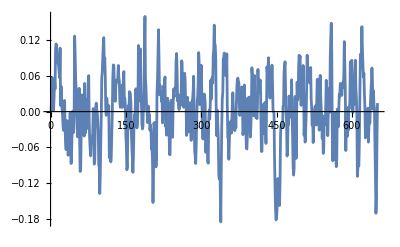

```mathematica
ListLinePlot[TM[[All,6]]]
```

```mathematica
Export["/Users/lha305/Desktop//NTMCRN.csv",TM]
```

/Users/lha305/Desktop//NTMCRN.csv

```mathematica
(* --------------   Tipping Model with Constant Red Noise ----------*)
TMCRN=List[];
Do[
Clear[x,F,t,tmax,zero,ans,data,Trend,NTrend,proc,n,F,t,s,noise,x2];
Clear[n,noise,phi,sigma,no,phio,sigmao];
Clear[x,F,t,tmax,zero,ans,data,Trend,NTrend,proc,n,F,t,s,noise,x2,ARe,AR,noise2,noisew];
F=(2/n)*t -1;
n=1000;
noise ={};
phi={};
sigma={};
no=0;
phio = 0.3;
sigmao=0.1;
Do[
AppendTo[noise,no];
phio = 0.3;
no = phio*no + RandomReal[NormalDistribution[0,sigmao]],
{i,0,n}];
cont=Interpolation[noise];
s=NDSolve[{x'[t]==-x[t]^3+x[t]-F+cont[t+1], x2'[t]==-x2[t]^3+x2[t]-F ,x[0]==1.25, x2[0]==1.25},{x,x2},{t,0,n}];
Clear[signal];
signal ={};
Do[
AppendTo[signal,Evaluate[x[i]/.s][[1]]],{i,0,650,1}];

TMCRN=AppendTo[TMCRN,signal];
,100]
```

{651,100}

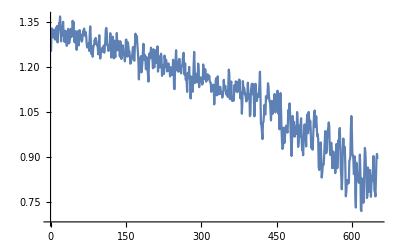

```mathematica
TM=Transpose[TMCRN];
Dimensions[TM]
ListLinePlot[TM[[All,1]]]
```

```mathematica
Export["/Users/lha305/Desktop//TMCRN.csv",TM]
```

/Users/lha305/Desktop//TMCRN.csv

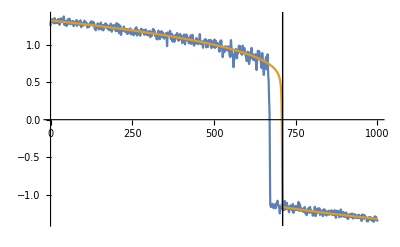

```mathematica
Plot[{Evaluate[x[t]/.s], Evaluate[x2[t]/.s]},{t,0,n},PlotRange->All,Epilog->{InfiniteLine[{710,0},{0,1}]}]
```